```mathematica
(*lattice size*)
L=80;

(*define coupling constant and their probability distribution*)
h=Array[0&,{L,1}];
PL= 0.95;
Bm=RandomVariate[UniformDistribution[{0,1}],L];
For[i8=1,i8<L+1,i8++,
If[Part[Bm,i8]< PL, h[[i8,1]]=1.6,h[[i8,1]]=0.1]
];
lambda1=0.4;
lambda2=-1.0;

(*initilize matrix*)
m=Array[0&,{L,L}];
For[i=1,i<L+1,i++,
For[j=1,j<L+1,j++,
Which[i==j,m[[i,i]]=h[[i,1]],j==i+1 ,m[[i,j]]=-lambda1,j==i+2 ,m[[i,j]]=-lambda2]
]
];

(* 2L * 2L Hamilitonian *)
A=0.5*(m+Transpose[m]);
B=0.5*(m-Transpose[m]);
H=ArrayFlatten[{{A,B},{-B,-A}}];
(*end*)
```

```mathematica
(*Eigenvector*)
eigenvalues=Eigenvalues[H];
eigenvectors=Eigenvectors[H];
(*make phase equal*)
eigenvectorsN=eigenvectors;
For[p=1,p<2L+1,p=p+2,
If[eigenvectors[[p,1]]*eigenvectors[[p+1,L+1]]<0,eigenvectorsN[[p+1]]=-eigenvectors[[p+1]],eigenvectorsN[[p+1]]=eigenvectors[[p+1]]]
];
(*find matrix phi and si*)
newEigenone=Array[0&,{L,L}];
newEigentwo=Array[0&,{L,L}];
For[q1=1,q1<L+1,q1++,
For[k1=1,k1<L+1,k1++,
newEigenone[[q1,k1]]=eigenvectorsN[[2q1-1,k1]]+eigenvectorsN[[2q1,k1]]
]
];
For[q2=1,q2<L+1,q2++,
If[Part[eigenvalues,2q2-1]< 0,
For[k2=1,k2<L+1,k2++,
newEigentwo[[q2,k2]]=-eigenvectorsN[[2q2-1,k2]]+eigenvectorsN[[2q2,k2]]
],
For[k2=1,k2<L+1,k2++,
newEigentwo[[q2,k2]]=eigenvectorsN[[2q2-1,k2]]-eigenvectorsN[[2q2,k2]]
]]
];
c=Array[0&,{L,1}];
phi=Array[0&,{L,L}]; 
si=Array[0&,{L,L}];
For[k=1,k<L+1,k++,
     c[[k,1]]=1;
phi[[All,k]]=Flatten[LinearSolve[newEigenone,c]];
   si[[All,k]]=Flatten[LinearSolve[newEigentwo,c]];
    c[[k,1]]=0
];
```

```mathematica
(*Calculate spin spin correlation function*)
G=Array[0&,{L,L}]; 
S=Array[0&,{L,L}]; 
CorF=Array[0&,{L,L}]; 
For[i1=1,i1<L+1,i1++,
For[j1=1,j1<L+1,j1++,
G[[i1,j1]]=-Sum[si[[μ,i1]]*phi[[μ,j1]],{μ,1,L}]
]
];
For[i2=1,i2<L+1,i2++,
For[j2=i2+1,j2<L+1,j2++,
s=Array[0&,{j2-i2,j2-i2}];
For[m2=1,m2<j2-i2+1,m2++,
For[n2=1,n2<j2-i2+1,n2++,
s[[m2,n2]]=G[[i2+m2-1,i2+n2]]
]
];
S[[i2,j2]]=Det[s]
]
];
CorF = IdentityMatrix[L]+S+Transpose[S];
```

```mathematica
(*Matrix Plot*)
MatrixPlot[Chop[CorF,0.01],PlotLegends->True]
```

-Graphics-

0.00822919

0.014785

0.0310216

0.0414563

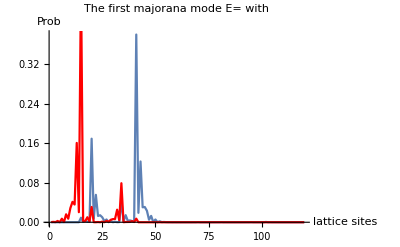

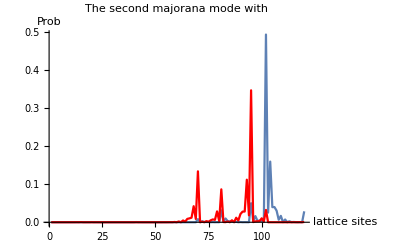

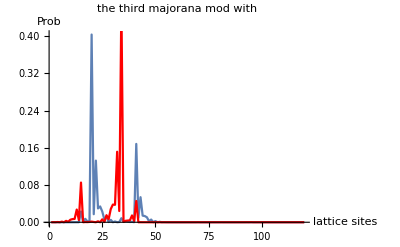

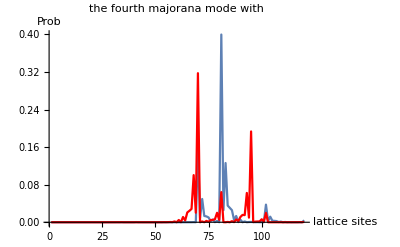

```mathematica
phi1=Array[0&,{L,L}];
Eg=Array[0&,{L,L}];
si1 =Array[0&,{L,L}];
{phi1,Eg,si1}=SingularValueDecomposition[m];
mj1=Array[0&,{L,1}];
mj2=Array[0&,{L,1}];
mj3=Array[0&,{L,1}];
mj4=Array[0&,{L,1}];
mj5=Array[0&,{L,1}];
mj6=Array[0&,{L,1}];
mj7=Array[0&,{L,1}];
mj8=Array[0&,{L,1}];
mj1=phi1[[All,L]];
mj2=si1[[All,L]];
mj3=phi1[[All,L-1]];
mj4=si1[[All,L-1]];
mj5=phi1[[All,L-2]];
mj6=si1[[All,L-2]];
mj7=phi1[[All,L-3]];
mj8=si1[[All,L-3]];
Eg[[L,L]]
Eg[[L-1,L-1]]
Eg[[L-2,L-2]]
Eg[[L-3,L-3]]
P1=ListLinePlot[mj1*mj1,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Re part of the first majorana mode",16]];
P2=ListLinePlot[mj2*mj2,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Im part of the first majorana mode",16],PlotStyle->Red,PlotRange->All];
Show[P1,P2,AxesLabel->{Style["lattice sites",11],Style["Prob",11]},PlotLabel->Style[" The first majorana mode E=  with "]]
P3=ListLinePlot[mj3*mj3,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Re part of the second majorana mode",16]];
P4=ListLinePlot[mj4*mj4,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Im part of the second majorana mode",16],PlotStyle->Red,PlotRange->All];
Show[P3,P4,AxesLabel->{Style["lattice sites",11],Style["Prob",11]},PlotLabel->Style[" The second majorana mode  with "]]
P5=ListLinePlot[mj5*mj5,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Re part of the third majorana mode",16]];
P6=ListLinePlot[mj6*mj6,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Im part of the third majorana mode",16],PlotStyle->Red,PlotRange->All];
Show[P5,P6,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style[" the third majorana mod  with "]]
P7=ListLinePlot[mj7*mj7,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Re part of the fourth majorana mode",16]];
P8=ListLinePlot[mj8*mj8,PlotRange->Full,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style["Im part of the fourth majorana mode",16],PlotStyle->Red,PlotRange->All];
Show[P7,P8,AxesLabel->{Style["lattice sites",13],Style["Prob",13]},PlotLabel->Style[" the fourth majorana mode  with "]]
```